## Walker’s Wolfram Language Cheat Sheet

/@ (Map)

```mathematica
Times[#,2]&/@{1,2,3,4,5}
```

{2,4,6,8,10}

@@ (Apply)

```mathematica
StringJoin@@{"party"," -- ","SO fun!"}
```

party -- SO fun!

@@@ (Map Apply)

```mathematica
StringJoin@@@{{"Is there...","a party?"},{"Or is there...","not?"}}
```

{Is there...a party?,Or is there...not?}

//

```mathematica
{"party"," -- ","SO fun!"}//StringJoin
```

party -- SO fun!

Manipulate

```mathematica
Manipulate[Times[m,2],{m,5}]
```

Table

```mathematica
Table[Times[n,2],{n,{1,2,3,4,5}}]
```

{2,4,6,8,10}

Array

```mathematica
Array[Times[#,2]&,5]
```

{2,4,6,8,10}

Module

```mathematica
Module[{x=2,y=3},x*y]
```

6

Style

```mathematica
Style["Party!",Pink,50]
```

Party!

Rasterize

```mathematica
Rasterize[Style["Party!",Pink,50]]
```

-Graphics-

Color Negate

```mathematica
ColorNegate[Rasterize[Style["Party!",Pink,50]]]
```

-Graphics-

Graphics + Regular Polygon

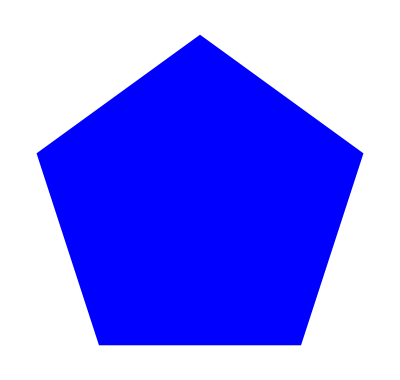

```mathematica
Graphics[Style[RegularPolygon[5],Blue]]
```

Image Add

```mathematica
ImageAdd[Graphics[Style[RegularPolygon[5],Blue]],Rasterize[Style["Party!",Pink,50]]]
```

-Graphics-

Point + Point Size

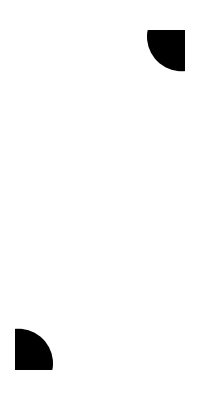

```mathematica
Graphics[{PointSize[0.3],
Point[{{1,1},{2,3}}]}]
```

Line

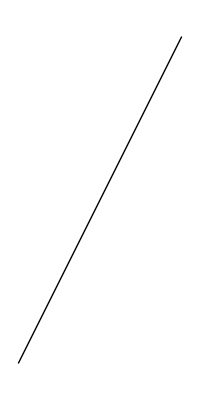

```mathematica
Graphics[Line[{{1,1},{2,3}}]]
```

End Points on a Line

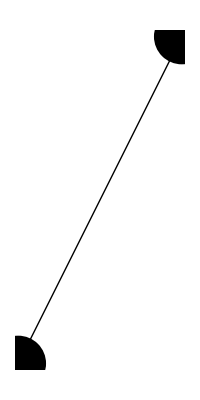

```mathematica
Graphics[{PointSize[0.1],
Point[{{1,1},{2,3}}],
Line[{{1,1},{2,3}}]
}]
```

Conditional Tests

```mathematica
10==2
10>2
10<2
```

False

True

False

Q Tests

```mathematica
IntegerQ[10]
MemberQ[{8,9,10},10]
PrimeQ[10]
NumberQ["10"]
LetterQ["10"]
```

True

True

False

False

False

If

```mathematica
If[PrimeQ[#],#,Nothing]&/@Range[23]
```

{2,3,5,7,11,13,17,19,23}